```mathematica
Notebook for the polynomial method in the Schroedinger equation. 
This example is for the case of the hexagonal well of side 1
```

Defining initialization variables

```mathematica
size=91;
L=1;
sqrt3=N[√3];
```

Symbolic integral of the generic x^n y^m integral term

```mathematica
$Assumptions={m≥0&&m∈Integers,n≥0&&n∈Integers,x∈Reals,y∈Reals};
integral[n_,m_]=1/((1+n) (2+m+n))2^(-2-m-n)* 3^((1+m)/2) (1+(-1)^m) (1+(-1)^n) (1+2^(2+m+n) (1+n) Beta[1/2,1+m,1+n]);
AbsoluteTiming[intTablehex=ParallelTable[N[integral[i,j],100],{i,0,200},{j,0,200},Method->"CoarsestGrained",DistributedContexts->Automatic];]
MyIntegral[n_,m_]:=MyIntegral[n,m]=intTablehex[[n+1,m+1]]
SetAttributes[MyIntegral,Listable]
AbsoluteTiming[ParallelTable[MyIntegral[i,j],{i,0,199},{j,0,199}];]
```

{3.8358,Null}

{0.366871,Null}

Creating data folder

```mathematica
shape="hexagon";
folder="~/agr_tese/data/symbolic_new_2/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
reg=Polygon[CirclePoints[L,6]];
```

Defining normalization, scalar product, and Hamiltonian integration elements

```mathematica
coeffs[func_]:=coeffs[func]=GroebnerBasis`DistributedTermsList[func,{x,y},MonomialOrder->DegreeLexicographic][[1,All]]
SetAttributes[coeffs,Listable]
MyNorm[func1_]:=√MyProd[func1,func1]

(*mylist[func1_,func2_]:=mylist[func1,func2]=Outer[Times,MonomialList[func1,"DegreeLexicographic"],MonomialList[func2,"DegreeLexicographic"]]//Flatten
MyProd[func1_,func2_]:=Collect[Dot[(Flatten[(coeffs[mylist[func1[x,y],func2[x,y]]])[[All,All,2]]]),MyIntegral[(Flatten[(coeffs[mylist[func1[x,y],func2[x,y]]])[[All,All,1,1]]]),(Flatten[(coeffs[mylist[func1[x,y],func2[x,y]]])[[All,All,1,2]]])]],{x,y},Simplify]
*)
MyProd[func1_,func2_]:=NIntegrate[func1[x,y]*func2[x,y],{y,-sqrt3/2*L,sqrt3/2*L},{x,-L+RealAbs[y]/sqrt3,L-RealAbs[y]/sqrt3},Method->{"LocalAdaptive",Method->"LobattoKronrodRule","SymbolicProcessing"->0.0001}]

Ham[f1_,f2_]:=(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])
En[func1_]:=-1*Inner[Times,(func1[[All,2]]),MyIntegral[func1[[All,1,1]],func1[[All,1,2]]],Plus]
```

Finding the numerical eigenvalues for comparison

```mathematica
exact=(4Tan[π/6])/6*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,size];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
(*AbsoluteTiming[Table[CoefficientRules[ϕn[5,x,y]*ϕn[7,x,y]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Simplify[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Expand[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]*)
```

Defining the initial function

```mathematica
ϕu[1,x_,y_]=(y-(√3)/2 L)*(y+(√3)/2 L)*(x-(√3)/3 y-L)*(x-(√3)/3 y+L)*(x+(√3)/3 y-L)*(x+(√3)/3 y+L);
ϕn[1,x_,y_]=Simplify[(1/(MyNorm[ϕu[1,#1,#2]&]))*ϕu[1,x,y]];
En[coeffs[N[Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]]]]//AbsoluteTiming
```

{0.001093,7.26185}

```mathematica
AbsoluteTiming[CoefficientRules[ϕn[1,x,y],{x,y}];]
AbsoluteTiming[AAA=GroebnerBasis`DistributedTermsList[ϕn[1,x,y],{x,y},MonomialOrder->DegreeLexicographic][[1,All]];]
```

{0.000532,Null}

{0.000381,Null}

```mathematica
f[m_,x_,y_]:=If[Mod[(m-1)-(Floor[√(m-1)])^2,2]==0,x^Floor[√(m-1)]*y^(((m-1)-(Floor[√(m-1)])^2)/2),x^(((m-1)-(Floor[√(m-1)])^2-1)/2)*y^Floor[√(m-1)]]
For[m=2,m<size+1,m++,
ϕu[m,x_,y_]=f[m,x,y]*ϕn[1,x,y]-ParallelSum[MyProd[f[m,#1,#2]*ϕn[1,#1,#2]&,ϕn[n,#1,#2]&]*ϕn[n,x,y],{n,1,m-1},DistributedContexts->Automatic,Method->"CoarsestGrained"];
ϕn[m,x_,y_]=Simplify[ϕu[m,x,y]/MyNorm[ϕu[m,#1,#2]&]];Print[m]]//AbsoluteTiming
Basis[x_,y_]=Table[ϕn[i,x,y],{i,1,size}];
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

$Aborted

91

Uncomment this table for verification of the orthogonality of the basis (this calculation is extremely slow due to the ammount of zeros, so it is commented out)

```mathematica
(*ortho=ParallelTable[MyProd[Basis[#1,#2][[b]]&,Basis[#1,#2][[c]]&],{b,1,size},{c,1,i},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];]
MatrixForm[orthofull]//Chop*)
```

Calculate the Hamiltonian matrix
It is Hermitian, so only the upper-triangular matrix is calculated

```mathematica
AbsoluteTiming[H=ParallelTable[Ham[ϕn[i,#1,#2]&,ϕn[j,#1,#2]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{3.36047,Null}

```mathematica
AbsoluteTiming[Hn=ParallelTable[coeffs[N[H[[i,j]],100]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
```

{41.7087,Null}

```mathematica
AbsoluteTiming[H2=ParallelTable[En[Hn[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=Chop[MapThread[Join,{H2,Rest/@Flatten[Conjugate[H2],{{2},{1}}]}]];]
MatrixForm[Hfull]
```

{10.1694,Null}

{0.001853,Null}

(7.26185 | 0 | 0 | 0 | -1.08305 | -1.19638 | 0 | 0 | -0.627748 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.09149 | -1.07201 | 0 | 0 | -0.122084 | -0.684322 | 0 | 0 | -0.191519 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.81679 | -0.744271 | 0 | 0 | -0.202297 | -0.537127 | 0 | 0 | -0.12606 | -0.234109 | 0 | 0 | -0.0148031 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.601953 | -0.534492
0 | 18.1913 | 0 | 0 | 0 | 0 | 0 | 0.275311 | 0 | 0.588567 | 0 | 0 | 0 | 0.806386 | 0 | 0 | 0 | 0 | 0 | -1.03558 | 0 | 0 | 0 | -0.684717 | 0 | -1.13719 | 0 | 0 | 0 | 0.629391 | 0 | 0 | 0 | -0.0477269 | 0 | 0 | 0 | 0 | 0 | -0.962795 | 0 | 0 | 0 | -0.659805 | 0 | 0 | 0 | 0.00384115 | 0 | -1.2671 | 0 | 0 | 0 | 0.462299 | 0 | 0 | 0 | -0.115356 | 0 | 0 | 0 | 0.0708145 | 0 | 0 | 0 | 0
0 | 0 | 18.1913 | 0 | 0 | 0 | 0.287244 | 0 | 0 | 0 | 0.582837 | 0 | 0 | 0 | -1.61693 | 0 | 0 | 0 | 0.0606453 | 0 | 0 | 0 | 0.0567326 | 0 | 0 | 0 | -0.702725 | 0 | 0 | 0 | -1.73281 | 0 | 0 | 0 | -0.321476 | 0 | 0 | 0 | 0.0668327 | 0 | 0 | 0 | -0.152377 | 0 | 0 | 0 | 0.0727452 | 0 | 0 | 0 | -0.645551 | 0 | 0 | 0 | -1.43245 | 0 | 0 | 0 | -0.476081 | 0 | 0 | 0 | -0.0196872 | 0 | 0 | 0
0 | 0 | 0 | 33.0359 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.3061 | 2.61734 | 0 | 0 | 0.226535 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.78532 | -1.52986 | 0 | 0 | 1.66896 | -1.20637 | 0 | 0 | 0.167048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.60125 | -1.73367 | 0 | 0 | 1.22326 | -1.60216 | 0 | 0 | 0.172502 | -0.177152 | 0 | 0 | 0.13381 | 0 | 0
-1.08305 | 0 | 0 | 0 | 35.5759 | 2.80583 | 0 | 0 | 3.83283 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.0792 | 0.36576 | 0 | 0 | 4.43138 | 0.45588 | 0 | 0 | -0.497248 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.548891 | 0.00546769 | 0 | 0 | 3.76665 | -0.414431 | 0 | 0 | 0.219388 | -0.477819 | 0 | 0 | 0.271145 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.922248 | -0.0247801
-1.19638 | 0 | 0 | 0 | 2.80583 | 36.1353 | 0 | 0 | 0.882721 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.06447 | 7.1017 | 0 | 0 | 2.60054 | -2.61543 | 0 | 0 | 0.255813 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.06876 | 2.75872 | 0 | 0 | 1.5276 | -3.33391 | 0 | 0 | 0.448523 | -0.509403 | 0 | 0 | 0.293136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.650979 | 1.63575
0 | 0 | 0.287244 | 0 | 0 | 0 | 57.645 | 0 | 0 | 0 | 3.8541 | 0 | 0 | 0 | 5.19294 | 0 | 0 | 0 | 17.7808 | 0 | 0 | 0 | 5.32145 | 0 | 0 | 0 | 0.177334 | 0 | 0 | 0 | 0.00171962 | 0 | 0 | 0 | -0.832121 | 0 | 0 | 0 | 9.6028 | 0 | 0 | 0 | 5.3368 | 0 | 0 | 0 | 1.19015 | 0 | 0 | 0 | -0.423815 | 0 | 0 | 0 | -1.11392 | 0 | 0 | 0 | -1.01461 | 0 | 0 | 0 | 0.221934 | 0 | 0 | 0
0 | 0.275311 | 0 | 0 | 0 | 0 | 0 | 51.5379 | 0 | 6.51475 | 0 | 0 | 0 | 7.34144 | 0 | 0 | 0 | 0 | 0 | 7.84657 | 0 | 0 | 0 | -1.3057 | 0 | 4.09129 | 0 | 0 | 0 | 5.13698 | 0 | 0 | 0 | 3.12376 | 0 | 0 | 0 | 0 | 0 | 0.229369 | 0 | 0 | 0 | -3.11563 | 0 | 0 | 0 | 0.245292 | 0 | 2.72732 | 0 | 0 | 0 | 3.4043 | 0 | 0 | 0 | 2.45677 | 0 | 0 | -2.00836×10^-10 | 1.02114 | 0 | 1.05611×10^-10 | 0 | 0
-0.627748 | 0 | 0 | 0 | 3.83283 | 0.882721 | 0 | 0 | 79.7012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.9131 | 3.33436 | 0 | 0 | 19.2899 | 18.1692 | 0 | 0 | 5.3271 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.55823 | -1.35989 | 0 | 0 | 14.2982 | 2.29785 | 0 | 0 | 8.25457 | 1.38649 | 0 | 0 | 1.90749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.09539 | -1.87416
0 | 0.588567 | 0 | 0 | 0 | 0 | 0 | 6.51475 | 0 | 62.4179 | 0 | 0 | 0 | 10.145 | 0 | 0 | 0 | 0 | 0 | 2.61806 | 0 | 0 | 0 | -1.84952 | 0 | 17.3347 | 0 | 0 | 0 | 11.3481 | 0 | 0 | 0 | -0.12369 | 0 | 0 | 0 | 0 | 0 | 0.54723 | 0 | 0 | 0 | -1.50491 | 0 | 0 | 0 | 0.602912 | 0 | 5.54469 | 0 | 0 | 0 | 9.98523 | 0 | 0 | 0 | 0.524966 | 0 | 0 | 0 | 0.791796 | 0 | 0 | 0 | 0
0 | 0 | 0.582837 | 0 | 0 | 0 | 3.8541 | 0 | 0 | 0 | 63.5658 | 0 | 0 | 0 | 0.147603 | 0 | 0 | 0 | 3.94773 | 0 | 0 | 0 | 3.57831 | 0 | 0 | 0 | 21.0368 | 0 | 0 | 0 | -4.76007 | 0 | 0 | 0 | 0.322855 | 0 | 0 | 0 | 2.36944 | 0 | 0 | 0 | 2.52946 | 0 | 0 | 0 | 1.73586 | 0 | 0 | 0 | 11.6214 | 0 | 0 | 0 | -5.6604 | 0 | 0 | 0 | -0.861947 | 0 | 0 | 0 | 0.594406 | 0 | 0 | 0
0 | 0 | 0 | 5.3061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 91.4387 | 13.1919 | 0 | 0 | 10.7508 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37.1125 | 2.44929 | 0 | 0 | 13.0164 | 3.69502 | 0 | 0 | -0.0800222 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.6542 | 0.156208 | 1.11395×10^-10 | 0 | 13.06 | 0.677809 | 4.84458×10^-10 | 0 | 2.4387 | 0.000246735 | -3.16002×10^-10 | 0 | 0.603121 | 0 | 0
0 | 0 | 0 | 2.61734 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.1919 | 83.4363 | 0 | 0 | 10.284 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.145 | 19.9915 | 0 | 0 | 12.4077 | 0.63684 | 0 | 0 | 4.45976 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.83495 | 5.95793 | 0 | 0 | 10.1419 | -5.36517 | 2.37659×10^-10 | 0 | 3.3204 | 2.29955 | 1.73878×10^-10 | -1.19008×10^-10 | 2.00716 | 0 | 0
0 | 0.806386 | 0 | 0 | 0 | 0 | 0 | 7.34144 | 0 | 10.145 | 0 | 0 | 0 | 118.663 | 0 | 0 | 0 | 0 | 0 | 14.6735 | 0 | 0 | 0 | 14.9953 | 0 | 18.5809 | 0 | 0 | 0 | 49.6381 | 0 | 0 | 0 | 15.0257 | 0 | 0 | 0 | 0 | 0 | 2.95202 | 0 | 0 | 0 | 5.14537 | 0 | 0 | 0 | -1.30768 | 0 | 12.2467 | 0 | 0 | 0 | 30.7231 | 0 | -4.0411×10^-10 | -3.22465×10^-10 | 17.4319 | 0 | -4.54018×10^-10 | -9.45961×10^-10 | 3.61988 | 0 | 9.57014×10^-10 | 0 | 0
0 | 0 | -1.61693 | 0 | 0 | 0 | 5.19294 | 0 | 0 | 0 | 0.147603 | 0 | 0 | 0 | 107.044 | 0 | 0 | 0 | 16.1232 | 0 | 0 | 0 | 21.1186 | 0 | 0 | 0 | 2.48176 | 0 | 0 | 0 | 28.5017 | 0 | 0 | 0 | 2.62612 | 0 | 0 | 0 | 7.9681 | 0 | 0 | 0 | 18.3897 | 0 | 0 | 0 | 10.4854 | 0 | 0 | 0 | -3.37087 | 0 | 0 | 0 | 7.69159 | 0 | 0 | 0 | -1.45046 | 0 | 0 | 0 | 2.79196 | 2.78126×10^-10 | 0 | 0
0 | 0 | 0 | 0.226535 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.7508 | 10.284 | 0 | 0 | 149.46 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.0089 | 14.4273 | 0 | 0 | 39.0879 | 50.7847 | 0 | 0 | 14.0536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0844 | -0.297941 | 1.4476×10^-10 | 0 | 35.0639 | 15.3994 | 1.41134×10^-9 | 0 | 21.0626 | 8.10798 | 7.27708×10^-10 | -5.5354×10^-10 | 5.34955 | 0 | 0
-1.09149 | 0 | 0 | 0 | 6.0792 | 2.06447 | 0 | 0 | 11.9131 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 98.2111 | 1.0654 | 0 | 0 | 19.0319 | 6.07996 | 0 | 0 | -2.19382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.8511 | -0.464499 | 0 | 0 | 21.9082 | 1.624 | 0 | 0 | 0.355151 | -1.71851 | 0 | 0 | 1.63563 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00252×10^-10 | 0 | 14.6065 | -0.433613
-1.07201 | 0 | 0 | 0 | 0.36576 | 7.1017 | 0 | 0 | 3.33436 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0654 | 103.072 | 0 | 0 | 5.87391 | 0.416376 | 0 | 0 | 4.32149 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.847602 | 44.5684 | 0 | 0 | 4.78716 | -7.57014 | 0 | 0 | 2.81584 | 1.89583 | 0 | 0 | 2.71031 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.463733 | 28.0723
0 | 0 | 0.0606453 | 0 | 0 | 0 | 17.7808 | 0 | 0 | 0 | 3.94773 | 0 | 0 | 0 | 16.1232 | 0 | 0 | 0 | 150.196 | 0 | 0 | 0 | 24.6001 | 0 | 0 | 0 | 2.96907 | 0 | 0 | 0 | 10.117 | 0 | 0 | 0 | -1.33648 | 0 | 0 | 0 | 72.3656 | 0 | 0 | 0 | 30.2992 | 0 | 0 | 0 | 3.39054 | 0 | 1.00326×10^-10 | 0 | -0.0409679 | 0 | 0 | 0 | 3.66667 | 0 | 0 | 0 | -1.58956 | 0 | 0 | 0 | 1.17628 | 1.55213×10^-10 | 0 | 0
0 | -1.03558 | 0 | 0 | 0 | 0 | 0 | 7.84657 | 0 | 2.61806 | 0 | 0 | 0 | 14.6735 | 0 | 0 | 0 | 0 | 0 | 122.391 | 0 | 0 | 0 | 8.8159 | 0 | 3.40702 | 0 | 0 | 0 | 17.4449 | 0 | 0 | 0 | 13.7298 | 0 | 0 | 0 | 0 | 0 | 41.2216 | 0 | 0 | 0 | -3.00793 | 0 | 0 | 0 | 5.29368 | 0 | 1.66 | 0 | 0 | 0 | 10.8845 | 0 | -1.52391×10^-10 | -1.06333×10^-10 | 13.1687 | 0 | -4.27441×10^-10 | -1.06256×10^-9 | 6.43312 | 0 | 1.50631×10^-10 | 0 | 0
-0.122084 | 0 | 0 | 0 | 4.43138 | 2.60054 | 0 | 0 | 19.2899 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.0319 | 5.87391 | 0 | 0 | 166.424 | 31.8982 | 0 | 0 | 19.9659 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.9139 | 3.55686 | 0 | 0 | 81.7941 | 6.73563 | 0 | 0 | 27.7711 | 9.62652 | 0 | 0 | -1.40276 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.7343 | 2.46243
-0.684322 | 0 | 0 | 0 | 0.45588 | -2.61543 | 0 | 0 | 18.1692 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.07996 | 0.416376 | 0 | 0 | 31.8982 | 167.074 | 0 | 0 | 30.3598 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.1674 | 0.463181 | 0 | 0 | 39.7878 | 52.9632 | 0 | 0 | 32.89 | 16.4197 | 1.17474×10^-10 | 0 | 13.9869 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.57346 | -6.9541
0 | 0 | 0.0567326 | 0 | 0 | 0 | 5.32145 | 0 | 0 | 0 | 3.57831 | 0 | 0 | 0 | 21.1186 | 0 | 0 | 0 | 24.6001 | 0 | 0 | 0 | 200.608 | 0 | 0 | 0 | 11.0396 | 0 | 0 | 0 | 32.9756 | 0 | 0 | 0 | 25.7467 | 0 | 0 | 0 | 33.0193 | 0 | 0 | 0 | 98.0255 | 0 | 0 | -1.901×10^-10 | 27.0828 | 0 | 1.42288×10^-10 | 0 | 5.2611 | 0 | 0 | 0 | 9.75587 | 0 | 0 | 0 | 12.0922 | 1.06348×10^-10 | 2.2562×10^-10 | 0 | -3.45973 | -6.58007×10^-10 | 0 | 0
0 | -0.684717 | 0 | 0 | 0 | 0 | 0 | -1.3057 | 0 | -1.84952 | 0 | 0 | 0 | 14.9953 | 0 | 0 | 0 | 0 | 0 | 8.8159 | 0 | 0 | 0 | 185.67 | 0 | -8.21667 | 0 | 0 | 0 | 31.4989 | 0 | 0 | 0 | 36.8897 | 0 | 0 | 0 | 0 | 0 | 14.6531 | 0 | 0 | 0 | 66.6043 | 0 | 0 | 0 | 9.77335 | 0 | -8.61976 | 0 | 0 | 0 | 13.5535 | 0 | -4.18177×10^-10 | -3.17625×10^-10 | 39.0731 | 0 | -1.12629×10^-9 | -2.68768×10^-9 | 22.0703 | 3.52323×10^-10 | -7.55925×10^-10 | 0 | 0
-0.191519 | 0 | 0 | 0 | -0.497248 | 0.255813 | 0 | 0 | 5.3271 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.19382 | 4.32149 | 0 | 0 | 19.9659 | 30.3598 | 0 | 0 | 238.875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -11.8737 | 12.0788 | 0 | 0 | 40.5661 | 35.1328 | 0 | 0 | 60.4619 | 98.4831 | 4.79691×10^-10 | 0 | 24.6752 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.60197×10^-10 | 0 | 0 | 0 | 0 | 0 | -13.0311 | 5.57373
0 | -1.13719 | 0 | 0 | 0 | 0 | 0 | 4.09129 | 0 | 17.3347 | 0 | 0 | 0 | 18.5809 | 0 | 0 | 0 | 0 | 0 | 3.40702 | 0 | 0 | 0 | -8.21667 | 0 | 145.713 | 0 | 0 | 0 | 30.5843 | 0 | 0 | 0 | -4.52833 | 0 | 0 | 0 | 0 | 0 | 0.464544 | 0 | 0 | 0 | -4.96254 | 0 | 0 | 0 | 1.76532 | 0 | 61.0655 | 0 | -1.02818×10^-10 | 0 | 35.5116 | 0 | -3.10068×10^-10 | -2.62462×10^-10 | -3.19437 | 0 | 2.12534×10^-10 | 7.20068×10^-10 | 1.79349 | 0 | -3.04945×10^-10 | 0 | 0
0 | 0 | -0.702725 | 0 | 0 | 0 | 0.177334 | 0 | 0 | 0 | 21.0368 | 0 | 0 | 0 | 2.48176 | 0 | 0 | 0 | 2.96907 | 0 | 0 | 0 | 11.0396 | 0 | 0 | 0 | 158.482 | 0 | 0 | 0 | -0.192794 | 0 | 0 | 0 | 5.74312 | 0 | 0 | 0 | 3.59225 | 0 | 0 | 0 | 9.53726 | 0 | 0 | 0 | 6.37067 | 0 | 0 | 0 | 81.1223 | 0 | 0 | 0 | -10.5993 | 0 | 0 | 0 | 2.03349 | 0 | 0 | 0 | 3.56922 | 2.55777×10^-10 | 0 | 0
0 | 0 | 0 | 2.78532 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37.1125 | 13.145 | 0 | 0 | 24.0089 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 217.965 | 7.89448 | 0 | 0 | 39.6283 | 17.7679 | 0 | 0 | -0.0448777 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 116.94 | -1.47596 | 5.2926×10^-10 | 0 | 50.191 | 6.84679 | 2.13499×10^-9 | 0 | 6.88364 | 0.306035 | -1.63787×10^-9 | 0 | 2.96185 | 1.04391×10^-10 | 0
0 | 0 | 0 | -1.52986 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.44929 | 19.9915 | 0 | 0 | 14.4273 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.89448 | 174.528 | 0 | 0 | 16.8989 | 15.7084 | 0 | 0 | 15.5955 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.00013 | 71.7501 | 0 | 0 | 19.2108 | -5.422 | 5.27936×10^-10 | 0 | 8.40898 | 13.6283 | 1.27336×10^-9 | -6.09537×10^-10 | 9.2419 | 0 | 0
0 | 0.629391 | 0 | 0 | 0 | 0 | 0 | 5.13698 | 0 | 11.3481 | 0 | 0 | 0 | 49.6381 | 0 | 0 | 0 | 0 | 0 | 17.4449 | 0 | 0 | 0 | 31.4989 | 0 | 30.5843 | 0 | 0 | 0 | 272.305 | 0 | 0 | 0 | 48.6427 | 0 | 0 | 0 | 0 | 0 | 14.6573 | 0 | 0 | 0 | 27.4502 | 0 | 0 | 0 | -0.71025 | 0 | 39.5736 | 0 | -1.87103×10^-10 | 0 | 150.841 | 0 | -1.82611×10^-9 | -1.44715×10^-9 | 66.52 | 0 | -1.589×10^-9 | -3.13153×10^-9 | 8.87768 | 0 | 4.37907×10^-9 | 0 | 0
0 | 0 | -1.73281 | 0 | 0 | 0 | 0.00171962 | 0 | 0 | 0 | -4.76007 | 0 | 0 | 0 | 28.5017 | 0 | 0 | 0 | 10.117 | 0 | 0 | 0 | 32.9756 | 0 | 0 | 0 | -0.192794 | 0 | 0 | 0 | 220.055 | 0 | 0 | 0 | 27.3499 | 0 | 0 | 0 | 8.97952 | 0 | 0 | 0 | 46.9578 | 0 | 0 | -1.15393×10^-10 | 29.7281 | 0 | 0 | 0 | -1.989 | 0 | 0 | 0 | 86.0675 | 0 | 0 | 0 | 11.2772 | 0 | 1.47484×10^-10 | 0 | 16.3537 | 1.06408×10^-9 | 0 | 0
0 | 0 | 0 | 1.66896 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.0164 | 12.4077 | 0 | 0 | 39.0879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39.6283 | 16.8989 | 0 | 0 | 262.533 | 56.1331 | 1.12006×10^-10 | 0 | 27.0158 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.17057×10^-10 | 0 | 0 | 0 | -1.49653×10^-10 | 0 | 0 | 0 | 46.6595 | 8.7835 | 6.09339×10^-10 | 0 | 142.72 | 11.9907 | 4.39118×10^-9 | -2.52739×10^-10 | 45.9334 | 13.1772 | 2.18842×10^-10 | -8.52957×10^-10 | -5.19666 | 0 | 0
0 | 0 | 0 | -1.20637 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.69502 | 0.63684 | 0 | 0 | 50.7847 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.7679 | 15.7084 | 0 | 0 | 56.1331 | 296.731 | 1.53221×10^-10 | 0 | 57.3437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.31474×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.4347 | 14.8813 | 5.2569×10^-10 | 0 | 84.6554 | 117.554 | 4.88406×10^-9 | -2.05254×10^-10 | 66.2649 | 45.6658 | 3.94292×10^-9 | -2.52371×10^-9 | 28.3476 | 0 | 0
0 | -0.0477269 | 0 | 0 | 0 | 0 | 0 | 3.12376 | 0 | -0.12369 | 0 | 0 | 0 | 15.0257 | 0 | 0 | 0 | 0 | 0 | 13.7298 | 0 | 0 | 0 | 36.8897 | 0 | -4.52833 | 0 | 0 | 0 | 48.6427 | 0 | 1.12006×10^-10 | 1.53221×10^-10 | 298.792 | 0 | -2.99639×10^-10 | 0 | 0 | 0 | 29.6547 | 0 | 0 | 0 | 51.9228 | 0 | 0 | 0 | 34.9631 | 0 | -16.4857 | 0 | 2.41759×10^-10 | 0 | 54.98 | 0 | -1.58649×10^-9 | -1.29636×10^-9 | 156.649 | 1.75731×10^-10 | -4.97778×10^-9 | -1.17098×10^-8 | 41.0503 | 5.91465×10^-10 | 5.79925×10^-9 | 0 | 0
0 | 0 | -0.321476 | 0 | 0 | 0 | -0.832121 | 0 | 0 | 0 | 0.322855 | 0 | 0 | 0 | 2.62612 | 0 | 0 | 0 | -1.33648 | 0 | 0 | 0 | 25.7467 | 0 | 0 | 0 | 5.74312 | 0 | 0 | 0 | 27.3499 | 0 | 0 | 0 | 285.177 | 0 | 0 | 0 | -12.5564 | 0 | 0 | 0 | 49.4805 | 0 | -1.23401×10^-10 | -3.47036×10^-10 | 50.5798 | 0 | 0 | 0 | 14.6404 | 0 | 0 | 0 | 37.8642 | 0 | 0 | 0 | 120.482 | 1.06676×10^-9 | 2.27068×10^-9 | -9.88643×10^-10 | 16.8671 | -2.11798×10^-9 | -2.21856×10^-10 | 0
0 | 0 | 0 | 0.167048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0800222 | 4.45976 | 0 | 0 | 14.0536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0448777 | 15.5955 | 0 | 0 | 27.0158 | 57.3437 | -2.99639×10^-10 | 0 | 346.062 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.63075×10^-10 | 0 | 0 | 0 | 9.02006×10^-10 | 0 | 0 | 0 | -14.6279 | 32.1538 | -1.02121×10^-9 | 0 | 56.5495 | 61.131 | 5.1587×10^-9 | -1.31416×10^-10 | 83.4091 | 156.649 | 1.57467×10^-8 | -7.10585×10^-9 | 34.8046 | 0 | 0
-0.81679 | 0 | 0 | 0 | 0.548891 | 1.06876 | 0 | 0 | 7.55823 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.8511 | 0.847602 | 0 | 0 | 27.9139 | 7.1674 | 0 | 0 | -11.8737 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 205. | -0.969789 | 0 | 0 | 45.7812 | 1.83387 | 0 | 0 | -5.77773 | -7.90311 | -1.06294×10^-10 | 0 | 3.03601 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.18305×10^-10 | 0 | 0 | 0 | 2.47247×10^-10 | 0 | 96.2183 | -0.746437
-0.744271 | 0 | 0 | 0 | 0.00546769 | 2.75872 | 0 | 0 | -1.35989 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.464499 | 44.5684 | 0 | 0 | 3.55686 | 0.463181 | 0 | 0 | 12.0788 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.969789 | 230.594 | 0 | 0 | 6.18056 | -3.33427 | 0 | 0 | 4.67587 | 10.7878 | 0 | 0 | 7.72389 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.899382 | 132.195
0 | 0 | 0.0668327 | 0 | 0 | 0 | 9.6028 | 0 | 0 | 0 | 2.36944 | 0 | 0 | 0 | 7.9681 | 0 | 0 | 0 | 72.3656 | 0 | 0 | 0 | 33.0193 | 0 | 0 | 0 | 3.59225 | 0 | 0 | 0 | 8.97952 | 0 | 0 | 0 | -12.5564 | 0 | 0 | 0 | 307.407 | 0 | 0 | 0 | 60.3004 | 0 | 0 | -1.26722×10^-10 | -1.68915 | 0 | 3.06156×10^-10 | 0 | 0.840119 | 0 | 0 | 0 | 3.58417 | 0 | 0 | 0 | -7.36515 | 0 | -1.88634×10^-10 | 0 | 1.12066 | 3.6378×10^-10 | 0 | 0
0 | -0.962795 | 0 | 0 | 0 | 0 | 0 | 0.229369 | 0 | 0.54723 | 0 | 0 | 0 | 2.95202 | 0 | 0 | 0 | 0 | 0 | 41.2216 | 0 | 0 | 0 | 14.6531 | 0 | 0.464544 | 0 | 0 | 0 | 14.6573 | 0 | 0 | 0 | 29.6547 | 0 | 0 | 0 | 0 | 0 | 247.475 | 0 | 0 | 0 | 17.4522 | 0 | 0 | 0 | 19.7889 | 0 | -1.67006 | 0 | 0 | 0 | 15.7096 | 0 | -4.33612×10^-10 | -2.62322×10^-10 | 32.4036 | 0 | -8.68578×10^-10 | -2.32326×10^-9 | 16.2194 | 2.5066×10^-10 | -3.77024×10^-10 | 0 | 0
-0.202297 | 0 | 0 | 0 | 3.76665 | 1.5276 | 0 | 0 | 14.2982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.9082 | 4.78716 | 0 | 0 | 81.7941 | 39.7878 | 0 | 0 | 40.5661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45.7812 | 6.18056 | 0 | 0 | 369.958 | 26.1217 | 1.81811×10^-10 | 0 | 72.4469 | 39.0802 | 0 | 0 | 0.806324 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.06077×10^-10 | 0 | 0 | 0 | 7.3684×10^-10 | 0 | 54.7299 | 4.58649
-0.537127 | 0 | 0 | 0 | -0.414431 | -3.33391 | 0 | 0 | 2.29785 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.624 | -7.57014 | 0 | 0 | 6.73563 | 52.9632 | 0 | 0 | 35.1328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.83387 | -3.33427 | 0 | 0 | 26.1217 | 290.741 | 1.71738×10^-10 | 0 | 34.6787 | 53.3993 | 1.42745×10^-10 | 0 | 33.0991 | 0 | 0 | 0 | 0 | 0 | 1.70277×10^-10 | 0 | 0 | 0 | -1.9126×10^-10 | 0 | 0 | 0 | 5.52088×10^-10 | 0 | 0.319824 | -7.21689
0 | 0 | -0.152377 | 0 | 0 | 0 | 5.3368 | 0 | 0 | 0 | 2.52946 | 0 | 0 | 0 | 18.3897 | 0 | 0 | 0 | 30.2992 | 0 | 0 | 0 | 98.0255 | 0 | 0 | 0 | 9.53726 | 0 | 0 | 0 | 46.9578 | 0 | 0 | 0 | 49.4805 | 0 | 0 | 0 | 60.3004 | 0 | 1.81811×10^-10 | 1.71738×10^-10 | 438.005 | 0 | -3.0394×10^-10 | -9.16073×10^-10 | 76.142 | 0 | 9.82718×10^-10 | 0 | 13.731 | 0 | 0 | 0 | 41.5463 | 0 | 0 | 0 | 52.0707 | 4.60505×10^-10 | 9.74142×10^-10 | -3.93467×10^-10 | 0.376256 | -1.55358×10^-9 | -1.15571×10^-10 | -2.03006×10^-10
0 | -0.659805 | 0 | 0 | 0 | 0 | 0 | -3.11563 | 0 | -1.50491 | 0 | 0 | 0 | 5.14537 | 0 | 0 | 0 | 0 | 0 | -3.00793 | 0 | 0 | 0 | 66.6043 | 0 | -4.96254 | 0 | 0 | 0 | 27.4502 | 0 | 1.17057×10^-10 | 1.31474×10^-10 | 51.9228 | 0 | -3.63075×10^-10 | 0 | 0 | 0 | 17.4522 | 0 | 0 | 0 | 364.367 | 0 | 0 | 0 | 52.453 | 0 | -12.536 | 0 | 2.93894×10^-10 | 0 | 21.347 | 0 | -1.20238×10^-9 | -1.02352×10^-9 | 89.6539 | 0 | -2.10509×10^-9 | -4.84994×10^-9 | 48.9091 | 8.66982×10^-10 | -3.95337×10^-9 | 0 | 0
-0.12606 | 0 | 0 | 0 | 0.219388 | 0.448523 | 0 | 0 | 8.25457 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.355151 | 2.81584 | 0 | 0 | 27.7711 | 32.89 | 0 | 0 | 60.4619 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23401×10^-10 | 0 | -5.77773 | 4.67587 | 0 | 0 | 72.4469 | 34.6787 | -3.0394×10^-10 | 0 | 378.793 | 79.7844 | 1.60335×10^-9 | 0 | 33.3151 | 0 | 0 | 0 | 0 | 0 | 2.36173×10^-10 | 0 | 0 | 0 | 2.09003×10^-9 | 0 | 0 | 0 | -2.74415×10^-9 | 0 | -21.0767 | 1.25572
-0.234109 | 0 | 0 | 0 | -0.477819 | -0.509403 | 0 | 0 | 1.38649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.71851 | 1.89583 | 0 | 0 | 9.62652 | 16.4197 | -1.901×10^-10 | 0 | 98.4831 | 0 | 0 | 0 | 0 | 0 | -1.15393×10^-10 | 0 | 0 | 0 | -3.47036×10^-10 | 0 | -7.90311 | 10.7878 | -1.26722×10^-10 | 0 | 39.0802 | 53.3993 | -9.16073×10^-10 | 0 | 79.7844 | 468.917 | 1.69736×10^-9 | 0 | 86.1503 | 0 | 0 | 0 | 0 | 2.29838×10^-10 | 0 | 0 | 0 | 0 | 2.58066×10^-9 | 0 | 0 | 0 | 6.37794×10^-10 | 0 | -20.9032 | 20.4905
0 | 0 | 0.0727452 | 0 | 0 | 0 | 1.19015 | 0 | 0 | 0 | 1.73586 | 0 | 0 | 0 | 10.4854 | 0 | 0 | 0 | 3.39054 | 0 | 0 | 1.17474×10^-10 | 27.0828 | 0 | 4.79691×10^-10 | 0 | 6.37067 | 0 | 0 | 0 | 29.7281 | 0 | 0 | 0 | 50.5798 | 0 | -1.06294×10^-10 | 0 | -1.68915 | 0 | 0 | 1.42745×10^-10 | 76.142 | 0 | 1.60335×10^-9 | 1.69736×10^-9 | 415.361 | 0 | -1.96135×10^-9 | 0 | 10.9652 | 0 | 0 | 1.11719×10^-10 | 52.3596 | 0 | 0 | -1.49548×10^-10 | 64.4286 | 5.58798×10^-10 | 1.20709×10^-9 | -4.33759×10^-10 | 40.7447 | 1.55544×10^-9 | -7.21787×10^-10 | 1.71546×10^-10
0 | 0.00384115 | 0 | 0 | 0 | 0 | 0 | 0.245292 | 0 | 0.602912 | 0 | 0 | 0 | -1.30768 | 0 | 0 | 0 | 0 | 0 | 5.29368 | 0 | 0 | 0 | 9.77335 | 0 | 1.76532 | 0 | 0 | 0 | -0.71025 | 0 | -1.49653×10^-10 | 0 | 34.9631 | 0 | 9.02006×10^-10 | 0 | 0 | 0 | 19.7889 | 0 | 0 | 0 | 52.453 | 0 | 0 | 0 | 402.16 | -1.79152×10^-10 | 9.88533 | 0 | -3.9216×10^-10 | 1.27851×10^-10 | -17.9101 | 0 | 2.60766×10^-9 | 1.86226×10^-9 | 67.2228 | 1.132×10^-10 | -5.5271×10^-9 | -1.52911×10^-8 | 60.8156 | 1.03348×10^-9 | -2.63921×10^-9 | 0 | 0
-0.0148031 | 0 | 0 | 0 | 0.271145 | 0.293136 | 0 | 0 | 1.90749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.63563 | 2.71031 | 1.00326×10^-10 | 0 | -1.40276 | 13.9869 | 1.42288×10^-10 | 0 | 24.6752 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.03601 | 7.72389 | 3.06156×10^-10 | 0 | 0.806324 | 33.0991 | 9.82718×10^-10 | 0 | 33.3151 | 86.1503 | -1.96135×10^-9 | -1.79152×10^-10 | 471.181 | 0 | 0 | 0 | 0 | 6.99508×10^-10 | -7.00769×10^-10 | 0 | 0 | 1.9877×10^-10 | -4.10534×10^-9 | 0 | 0 | 0 | 6.33533×10^-9 | 0 | 11.3503 | 12.8296
0 | -1.2671 | 0 | 0 | 0 | 0 | 0 | 2.72732 | 0 | 5.54469 | 0 | 0 | 0 | 12.2467 | 0 | 0 | 0 | 0 | 0 | 1.66 | 0 | 0 | 0 | -8.61976 | 0 | 61.0655 | 0 | 0 | 0 | 39.5736 | 0 | 0 | 0 | -16.4857 | 0 | 0 | 0 | 0 | 0 | -1.67006 | 0 | 0 | 0 | -12.536 | 0 | 0 | 0 | 9.88533 | 0 | 279.268 | 0 | -4.44579×10^-10 | 0 | 62.3079 | 0 | -3.33602×10^-10 | -3.29007×10^-10 | -14.8134 | 0 | 5.20762×10^-10 | 1.61883×10^-9 | 4.052 | 0 | -1.04178×10^-9 | -1.32641×10^-10 | 0
0 | 0 | -0.645551 | 0 | 0 | 0 | -0.423815 | 0 | 0 | 0 | 11.6214 | 0 | 0 | 0 | -3.37087 | 0 | 0 | 0 | -0.0409679 | 0 | 0 | 0 | 5.2611 | 0 | 0 | 0 | 81.1223 | 0 | 0 | 0 | -1.989 | 0 | 0 | 0 | 14.6404 | 0 | 0 | 0 | 0.840119 | 0 | 0 | 0 | 13.731 | 0 | 0 | 0 | 10.9652 | 0 | 0 | 0 | 323.872 | 0 | 0 | 0 | -5.44373 | 0 | 0 | 0 | 12.8778 | 0 | 2.06549×10^-10 | -1.05054×10^-10 | 9.22342 | 4.7133×10^-10 | 0 | 2.76086×10^-10
0 | 0 | 0 | 1.60125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.6542 | 7.83495 | 0 | 0 | 12.0844 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.02818×10^-10 | 0 | 116.94 | 7.00013 | -1.87103×10^-10 | 0 | 46.6595 | 15.4347 | 2.41759×10^-10 | 0 | -14.6279 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.93894×10^-10 | 0 | 0 | 0 | -3.9216×10^-10 | 0 | -4.44579×10^-10 | 0 | 413.075 | -2.45601 | 1.82729×10^-9 | 0 | 85.2889 | 7.10907 | 4.44581×10^-9 | 0 | 0.552766 | -7.12747 | -5.68291×10^-9 | 4.32172×10^-10 | 3.09264 | 3.62696×10^-10 | 0
0 | 0 | 0 | -1.73367 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.156208 | 5.95793 | 0 | 0 | -0.297941 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.47596 | 71.7501 | 0 | 0 | 8.7835 | 14.8813 | 0 | 0 | 32.1538 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.27851×10^-10 | 0 | 0 | 0 | -2.45601 | 334.053 | 1.36551×10^-10 | 0 | 19.6747 | 15.139 | 9.44393×10^-10 | 0 | 10.6392 | 37.2112 | 3.33605×10^-9 | -1.53897×10^-9 | 19.25 | 0 | 0
0 | 0.462299 | 0 | 0 | 0 | 0 | 0 | 3.4043 | 0 | 9.98523 | 0 | 1.11395×10^-10 | 0 | 30.7231 | 0 | 1.4476×10^-10 | 0 | 0 | 0 | 10.8845 | 0 | 0 | 0 | 13.5535 | 0 | 35.5116 | 0 | 5.2926×10^-10 | 0 | 150.841 | 0 | 6.09339×10^-10 | 5.2569×10^-10 | 54.98 | 0 | -1.02121×10^-9 | 0 | 0 | 0 | 15.7096 | 0 | 0 | 0 | 21.347 | 0 | 2.29838×10^-10 | 1.11719×10^-10 | -17.9101 | 6.99508×10^-10 | 62.3079 | 0 | 1.82729×10^-9 | 1.36551×10^-10 | 506.313 | 0 | -5.7805×10^-9 | -5.24113×10^-9 | 112.533 | 0 | -1.35413×10^-9 | 0 | 1.82149 | -3.93351×10^-10 | 9.51267×10^-9 | 5.16108×10^-10 | 0
0 | 0 | -1.43245 | 0 | 0 | 0 | -1.11392 | 0 | 0 | 0 | -5.6604 | 0 | 0 | 0 | 7.69159 | 0 | 0 | 0 | 3.66667 | 0 | 0 | 0 | 9.75587 | 0 | 0 | 0 | -10.5993 | 0 | 0 | 0 | 86.0675 | 0 | 0 | 0 | 37.8642 | 0 | 0 | 0 | 3.58417 | 0 | 0 | 1.70277×10^-10 | 41.5463 | 0 | 2.36173×10^-10 | 0 | 52.3596 | 0 | -7.00769×10^-10 | 0 | -5.44373 | 0 | 0 | 0 | 388.469 | 3.03828×10^-10 | 1.30188×10^-10 | -1.95251×10^-10 | 59.2019 | 3.48479×10^-10 | 8.22245×10^-10 | -3.39901×10^-10 | 40.7035 | 1.77297×10^-9 | -2.26352×10^-10 | 0
0 | 0 | 0 | 1.22326 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.06 | 10.1419 | -4.0411×10^-10 | 0 | 35.0639 | 0 | 0 | 0 | -1.52391×10^-10 | 0 | 0 | 0 | -4.18177×10^-10 | 0 | -3.10068×10^-10 | 0 | 50.191 | 19.2108 | -1.82611×10^-9 | 0 | 142.72 | 84.6554 | -1.58649×10^-9 | 0 | 56.5495 | 0 | 0 | 0 | -4.33612×10^-10 | 0 | 0 | 0 | -1.20238×10^-9 | 0 | 0 | 0 | 2.60766×10^-9 | 0 | -3.33602×10^-10 | 0 | 85.2889 | 19.6747 | -5.7805×10^-9 | 3.03828×10^-10 | 565.624 | 58.5651 | 1.76771×10^-8 | -9.75099×10^-10 | 112.213 | 61.6221 | -1.97985×10^-9 | -2.46535×10^-9 | 1.61164 | 1.47185×10^-10 | 0
0 | 0 | 0 | -1.60216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.677809 | -5.36517 | -3.22465×10^-10 | 0 | 15.3994 | 0 | 0 | 0 | -1.06333×10^-10 | 0 | 0 | 0 | -3.17625×10^-10 | 0 | -2.62462×10^-10 | 0 | 6.84679 | -5.422 | -1.44715×10^-9 | 0 | 11.9907 | 117.554 | -1.29636×10^-9 | 0 | 61.131 | 0 | 0 | 0 | -2.62322×10^-10 | 0 | 0 | 0 | -1.02352×10^-9 | 0 | 0 | 0 | 1.86226×10^-9 | 0 | -3.29007×10^-10 | 0 | 7.10907 | 15.139 | -5.24113×10^-9 | 1.30188×10^-10 | 58.5651 | 467.95 | 1.08205×10^-8 | -3.17547×10^-10 | 61.3319 | 111.829 | 5.5341×10^-9 | -4.72538×10^-9 | 53.8889 | 0 | 0
0 | -0.115356 | 0 | 0 | 0 | 0 | 0 | 2.45677 | 0 | 0.524966 | 0 | 4.84458×10^-10 | 2.37659×10^-10 | 17.4319 | 0 | 1.41134×10^-9 | 0 | 0 | 0 | 13.1687 | 0 | 0 | 0 | 39.0731 | 0 | -3.19437 | 0 | 2.13499×10^-9 | 5.27936×10^-10 | 66.52 | 0 | 4.39118×10^-9 | 4.88406×10^-9 | 156.649 | 0 | 5.1587×10^-9 | 0 | 0 | 0 | 32.4036 | 0 | 0 | 0 | 89.6539 | 0 | 0 | -1.49548×10^-10 | 67.2228 | 1.9877×10^-10 | -14.8134 | 0 | 4.44581×10^-9 | 9.44393×10^-10 | 112.533 | -1.95251×10^-10 | 1.76771×10^-8 | 1.08205×10^-8 | 635.563 | 7.29809×10^-10 | -1.82312×10^-8 | -5.38546×10^-8 | 106.729 | 1.43509×10^-9 | 4.22553×10^-8 | -1.38644×10^-10 | 0
0 | 0 | -0.476081 | 0 | 0 | 0 | -1.01461 | 0 | 0 | 0 | -0.861947 | 0 | 0 | 0 | -1.45046 | 0 | 0 | 0 | -1.58956 | 0 | 0 | 0 | 12.0922 | 0 | 5.60197×10^-10 | 0 | 2.03349 | 0 | 0 | 0 | 11.2772 | -2.52739×10^-10 | -2.05254×10^-10 | 1.75731×10^-10 | 120.482 | -1.31416×10^-10 | -2.18305×10^-10 | 0 | -7.36515 | 0 | -2.06077×10^-10 | -1.9126×10^-10 | 52.0707 | 0 | 2.09003×10^-9 | 2.58066×10^-9 | 64.4286 | 1.132×10^-10 | -4.10534×10^-9 | 0 | 12.8778 | 0 | 0 | 0 | 59.2019 | -9.75099×10^-10 | -3.17547×10^-10 | 7.29809×10^-10 | 552.289 | 4.70048×10^-9 | 1.03303×10^-8 | -4.49403×10^-9 | 77.2105 | -9.75508×10^-9 | -1.57983×10^-9 | 2.6918×10^-10
0 | 0 | 0 | 0.172502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.4387 | 3.3204 | -4.54018×10^-10 | 0 | 21.0626 | 0 | 0 | 0 | -4.27441×10^-10 | 0 | 0 | 1.06348×10^-10 | -1.12629×10^-9 | 0 | 2.12534×10^-10 | 0 | 6.88364 | 8.40898 | -1.589×10^-9 | 0 | 45.9334 | 66.2649 | -4.97778×10^-9 | 1.06676×10^-9 | 83.4091 | 0 | 0 | 0 | -8.68578×10^-10 | 0 | 0 | 4.60505×10^-10 | -2.10509×10^-9 | 0 | 0 | 5.58798×10^-10 | -5.5271×10^-9 | 0 | 5.20762×10^-10 | 0 | 0.552766 | 10.6392 | -1.35413×10^-9 | 3.48479×10^-10 | 112.213 | 61.3319 | -1.82312×10^-8 | 4.70048×10^-9 | 521.546 | 102.734 | 2.46179×10^-8 | -1.18703×10^-8 | 38.6817 | 0 | 0
0 | 0 | 0 | -0.177152 | 0 | 0 | 0 | -2.00836×10^-10 | 0 | 0 | 0 | 0.000246735 | 2.29955 | -9.45961×10^-10 | 0 | 8.10798 | 0 | 0 | 0 | -1.06256×10^-9 | 0 | 0 | 2.2562×10^-10 | -2.68768×10^-9 | 0 | 7.20068×10^-10 | 0 | 0.306035 | 13.6283 | -3.13153×10^-9 | 1.47484×10^-10 | 13.1772 | 45.6658 | -1.17098×10^-8 | 2.27068×10^-9 | 156.649 | 0 | 0 | -1.88634×10^-10 | -2.32326×10^-9 | 0 | 0 | 9.74142×10^-10 | -4.84994×10^-9 | 0 | 0 | 1.20709×10^-9 | -1.52911×10^-8 | 0 | 1.61883×10^-9 | 2.06549×10^-10 | -7.12747 | 37.2112 | 0 | 8.22245×10^-10 | 61.6221 | 111.829 | -5.38546×10^-8 | 1.03303×10^-8 | 102.734 | 672.095 | 5.29069×10^-8 | -2.52567×10^-8 | 112.408 | 0 | 0
0 | 0.0708145 | 0 | 0 | 0 | 0 | 0 | 1.02114 | 0 | 0.791796 | 0 | -3.16002×10^-10 | 1.73878×10^-10 | 3.61988 | 0 | 7.27708×10^-10 | 0 | 0 | 0 | 6.43312 | 0 | 0 | 0 | 22.0703 | 0 | 1.79349 | 0 | -1.63787×10^-9 | 1.27336×10^-9 | 8.87768 | 0 | 2.18842×10^-10 | 3.94292×10^-9 | 41.0503 | -9.88643×10^-10 | 1.57467×10^-8 | 0 | 0 | 0 | 16.2194 | 0 | 0 | -3.93467×10^-10 | 48.9091 | 0 | 0 | -4.33759×10^-10 | 60.8156 | 0 | 4.052 | -1.05054×10^-10 | -5.68291×10^-9 | 3.33605×10^-9 | 1.82149 | -3.39901×10^-10 | -1.97985×10^-9 | 5.5341×10^-9 | 106.729 | -4.49403×10^-9 | 2.46179×10^-8 | 5.29069×10^-8 | 553.289 | 8.25044×10^-9 | -6.16238×10^-8 | -2.60269×10^-10 | 0
0 | 0 | -0.0196872 | 0 | 0 | 0 | 0.221934 | 0 | 0 | 0 | 0.594406 | 0 | -1.19008×10^-10 | 0 | 2.79196 | -5.5354×10^-10 | 1.00252×10^-10 | 0 | 1.17628 | 0 | 0 | 0 | -3.45973 | 3.52323×10^-10 | 0 | 0 | 3.56922 | 0 | -6.09537×10^-10 | 0 | 16.3537 | -8.52957×10^-10 | -2.52371×10^-9 | 5.91465×10^-10 | 16.8671 | -7.10585×10^-9 | 2.47247×10^-10 | 0 | 1.12066 | 2.5066×10^-10 | 7.3684×10^-10 | 5.52088×10^-10 | 0.376256 | 8.66982×10^-10 | -2.74415×10^-9 | 6.37794×10^-10 | 40.7447 | 1.03348×10^-9 | 6.33533×10^-9 | 0 | 9.22342 | 4.32172×10^-10 | -1.53897×10^-9 | -3.93351×10^-10 | 40.7035 | -2.46535×10^-9 | -4.72538×10^-9 | 1.43509×10^-9 | 77.2105 | -1.18703×10^-8 | -2.52567×10^-8 | 8.25044×10^-9 | 538.725 | 3.84643×10^-8 | 2.15806×10^-9 | 6.24442×10^-10
0 | 0 | 0 | 0.13381 | 0 | 0 | 0 | 1.05611×10^-10 | 0 | 0 | 0 | 0.603121 | 2.00716 | 9.57014×10^-10 | 2.78126×10^-10 | 5.34955 | 0 | 0 | 1.55213×10^-10 | 1.50631×10^-10 | 0 | 0 | -6.58007×10^-10 | -7.55925×10^-10 | 0 | -3.04945×10^-10 | 2.55777×10^-10 | 2.96185 | 9.2419 | 4.37907×10^-9 | 1.06408×10^-9 | -5.19666 | 28.3476 | 5.79925×10^-9 | -2.11798×10^-9 | 34.8046 | 0 | 0 | 3.6378×10^-10 | -3.77024×10^-10 | 0 | 0 | -1.55358×10^-9 | -3.95337×10^-9 | 0 | 0 | 1.55544×10^-9 | -2.63921×10^-9 | 0 | -1.04178×10^-9 | 4.7133×10^-10 | 3.09264 | 19.25 | 9.51267×10^-9 | 1.77297×10^-9 | 1.61164 | 53.8889 | 4.22553×10^-8 | -9.75508×10^-9 | 38.6817 | 112.408 | -6.16238×10^-8 | 3.84643×10^-8 | 619.827 | -3.01169×10^-10 | 0
-0.601953 | 0 | 0 | 0 | -0.922248 | 0.650979 | 0 | 0 | 5.09539 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.6065 | 0.463733 | 0 | 0 | 18.7343 | 3.57346 | 0 | 0 | -13.0311 | 0 | 0 | 1.04391×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | -2.21856×10^-10 | 0 | 96.2183 | -0.899382 | 0 | 0 | 54.7299 | 0.319824 | -1.15571×10^-10 | 0 | -21.0767 | -20.9032 | -7.21787×10^-10 | 0 | 11.3503 | -1.32641×10^-10 | 0 | 3.62696×10^-10 | 0 | 5.16108×10^-10 | -2.26352×10^-10 | 1.47185×10^-10 | 0 | -1.38644×10^-10 | -1.57983×10^-9 | 0 | 0 | -2.60269×10^-10 | 2.15806×10^-9 | -3.01169×10^-10 | 367.848 | -1.13872
-0.534492 | 0 | 0 | 0 | -0.0247801 | 1.63575 | 0 | 0 | -1.87416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.433613 | 28.0723 | 0 | 0 | 2.46243 | -6.9541 | 0 | 0 | 5.57373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.746437 | 132.195 | 0 | 0 | 4.58649 | -7.21689 | -2.03006×10^-10 | 0 | 1.25572 | 20.4905 | 1.71546×10^-10 | 0 | 12.8296 | 0 | 2.76086×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.6918×10^-10 | 0 | 0 | 0 | 6.24442×10^-10 | 0 | -1.13872 | 439.228)

Obtaining the numerical eigenvalues and eigenvectors

```mathematica
eval=Eigenvalues[Hfull];//AbsoluteTiming
evec=Eigenvectors[Hfull];
```

{0.000498,Null}

Plotting the eigenvalues

{2.90027,7.34907,7.34962,13.1534,13.1544,15.197,19.3093,21.3335,24.3632,24.3642,28.4304,28.4318,35.4826,35.4835,36.5135,38.2684,38.3592,45.1335,49.366,49.9352,50.5406,51.3459,51.6011,59.9901,59.9983,63.1301,63.2317,68.4685,69.8563,71.2549,77.8232,78.199,80.9542,81.3192,93.1113,94.1003,98.8729,105.524,110.546,111.348,113.616,115.592,118.6,139.182,139.199,139.438,143.673,149.806,156.258,156.884,160.776,177.97,179.573,188.389,188.539,190.871,197.859,206.038,218.264,222.716,241.884,272.445,281.628,306.357,362.081,409.093}

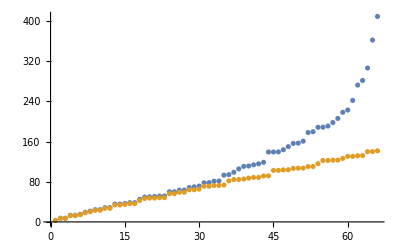

```mathematica
Sort[Abs[eval]/(π^2/4)]
ListPlot[{Sort[Abs[eval]/(π^2/4)],exact}]
```

Defining the eigenbasis

```mathematica
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

{1.11387,Null}

Comparing eigenvalues

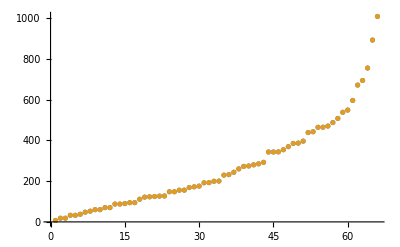

```mathematica
AAAA=Sort[Table[(Conjugate[evec].Hfull.Transpose[evec])[[i,i]],{i,1,size}]];
ListPlot[{AAAA,Sort[Re[Abs[eval]]]}]
```

Exporting the data

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[Abs[eval]]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",Table[mode[aa,x,y],{aa,1,size}]]
```

~/agr_tese/data/symbolic_new_2/schrodinger/hexagon_66/eigenvalues.dat

~/agr_tese/data/symbolic_new_2/schrodinger/hexagon_66/basis.m

~/agr_tese/data/symbolic_new_2/schrodinger/hexagon_66/eigenvectors.m

~/agr_tese/data/symbolic_new_2/schrodinger/hexagon_66/full_hamiltonian.m

~/agr_tese/data/symbolic_new_2/schrodinger/hexagon_66/eigenfunctions.m

Plotting the eigenfunctions

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```